```mathematica
(*Метод Монте-Карло*)
(*f(Subscript[x, 1],...,Subscript[x, d])=Subscript[x, 1]^2,...,Subscript[x, d]*)
(*I=∫_([0,1]^d) f(x)ⅆx = (∫...∫)_([0,1]^d)f(Subscript[x, 1],...,Subscript[x, d])ⅆ Subscript[x, 1]...ⅆ Subscript[x, d]=∫_0^1 Subscript[x, 1]^2 ⅆ Subscript[x, 1]∫_0^1 Subscript[x, 2] ⅆ Subscript[x, 2]....∫_0^1 Subscript[x, d] ⅆ Subscript[x, d]*)
(*∫_0^1 Subscript[x, i] ⅆ Subscript[x, i]=1/2 & ∫_0^1 Subscript[x, 1]^2 ⅆ Subscript[x, 1]=1/3 => I = 1/3*1/2^(d-1)*)
```

```mathematica
(*Задаем размерность*)
d=3;
RealIntVal = (∫_0^1 x^2 ⅆx)(∫_0^1 xⅆx)^(d-1);
Print["Значение интеграла равняется: ", N[RealIntVal]]
(*Количество случайных значений для каждой из переменных*)
NUMS={500, 1000, 2000, 5000, 10000, 25000, 50000, 100000};
(*Список для хранения посчитанных интегралов методом Монте-Карло*)
INT = List[];
INT2=List[];
(*Список для абсолютных ошибок*)
TotalErrors = List[];
(*Цикл по значеним заданным в NUMS*)
For[i = 1, i <= Length[NUMS], i++,
(*Генерируем матрицу n x d произвольных значений равномерно распредленных на от резке [0, 1]*)
(*По n значений для каждой из переменных*)
RandomValues = Table[RandomVariate[UniformDistribution[{0,1}],NUMS[[i]]],{k, 1,d}];
(*Переменная для суммы*)
SUM=0;
SUM2=0;
For[n = 1, n ≤ NUMS[[i]], n++,
FuncValue= (RandomValues[[1,n]])^2 *∏_(j=2)^d RandomValues[[j,n]];
FuncValue2= (RandomValues[[1,n]])^4 *∏_(j=2)^d (RandomValues[[j,n]])^2;
SUM = SUM + FuncValue;
SUM2=SUM2+ FuncValue2;
];
(*Добавляем значение интеграла в список*)
AppendTo[INT, SUM / NUMS[[i]]];
AppendTo[INT2, SUM2 / NUMS[[i]]];
AppendTo[TotalErrors,Abs[INT[[i]]-RealIntVal]]
]

For[i=1, i ≤ Length[NUMS],i++,
σ=√(INT2[[i]]-(INT[[i]])^2);
Print["При n = ", NUMS[[i]]];
Print["Интеграл по методу Мнте-Карло равен ",INT[[i]]];
Print["Абсолютная ошибка равна: ", TotalErrors[[i]]];
Print["σ(f) = ", σ];
Print["e^ran = ", σ/(√NUMS[[i]])];
]
```

Значение интеграла равняется: 0.0833333

При n = 500

Интеграл по методу Мнте-Карло равен 0.0818697

Абсолютная ошибка равна: 0.00146363

σ(f) = 0.117924

e^ran = 0.00527371

При n = 1000

Интеграл по методу Мнте-Карло равен 0.0868123

Абсолютная ошибка равна: 0.00347896

σ(f) = 0.126439

e^ran = 0.00399835

При n = 2000

Интеграл по методу Мнте-Карло равен 0.0854586

Абсолютная ошибка равна: 0.00212527

σ(f) = 0.122514

e^ran = 0.0027395

При n = 5000

Интеграл по методу Мнте-Карло равен 0.0833592

Абсолютная ошибка равна: 0.0000259033

σ(f) = 0.123663

e^ran = 0.00174886

При n = 10000

Интеграл по методу Мнте-Карло равен 0.0829236

Абсолютная ошибка равна: 0.000409717

σ(f) = 0.124162

e^ran = 0.00124162

При n = 25000

Интеграл по методу Мнте-Карло равен 0.082818

Абсолютная ошибка равна: 0.000515368

σ(f) = 0.122367

e^ran = 0.000773916

При n = 50000

Интеграл по методу Мнте-Карло равен 0.0832761

Абсолютная ошибка равна: 0.0000572197

σ(f) = 0.12363

e^ran = 0.000552892

При n = 100000

Интеграл по методу Мнте-Карло равен 0.0836856

Абсолютная ошибка равна: 0.000352271

σ(f) = 0.124235

e^ran = 0.000392866

```mathematica
(*При заданном ε найти минимальное n(ε),при котором ошибка e^ran(f) не больше ε*)
ϵ=0.005;
int=1;
int2=10;
nϵ=1;
While[(√(int2-int^2))/(√nϵ)> ϵ,
nϵ=nϵ+1;
int=0;
int2=0;
RandomValues = Table[RandomVariate[UniformDistribution[{0,1}],nϵ],{k, 1,d}];
For[n = 1, n ≤nϵ, n++,
FuncValue= (RandomValues[[1,n]])^2 *∏_(j=2)^d RandomValues[[j,n]];
FuncValue2= (RandomValues[[1,n]])^4 *∏_(j=2)^d (RandomValues[[j,n]])^2;
int=int + FuncValue;
int2=int2+FuncValue2;
];
int = int/nϵ;
int2=int2/nϵ;
];
Print["n(",ϵ,") = ", nϵ]
```

n(0.005) = 478

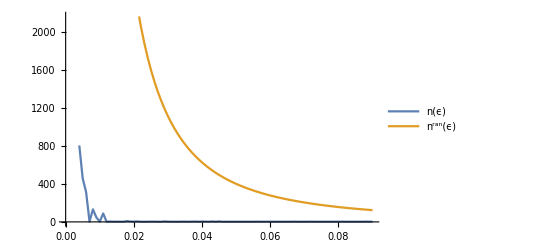

```mathematica
(*Построить график зависимости n(ε) от ε.Ис.02пользуя лишь знание σ(f) ≤ 1,построить (в той же системе координат) график зависимости оценки для n^ran(ε) от ε.*)
errors=List[];
neps=List[];
nran=List[];
For[ϵ=0.09, ϵ≥ 0.003,ϵ=ϵ-0.001,
int=1;
int2=10;
nϵ=1;
While[(√(int2-int^2))/(√nϵ)> ϵ,
nϵ=nϵ+1;
int=0;
int2=0;
RandomValues = Table[RandomVariate[UniformDistribution[{0,1}],nϵ],{k, 1,d}];
For[n = 1, n ≤nϵ, n++,
FuncValue= (RandomValues[[1,n]])^2 *∏_(j=2)^d RandomValues[[j,n]];
FuncValue2= (RandomValues[[1,n]])^4 *∏_(j=2)^d (RandomValues[[j,n]])^2;
int=int + FuncValue;
int2=int2+FuncValue2;
];
int = int/nϵ;
int2=int2/nϵ;
];
AppendTo[errors,ϵ];
AppendTo[neps,nϵ];
AppendTo[nran,1/ϵ^2];
]
LP1=Table[{errors[[i]],neps[[i]]},{i,1,Length[errors]}];
LP2=Table[{errors[[i]],nran[[i]]},{i,1,Length[errors]}];
ListLinePlot[{LP1,LP2},PlotLegends->{"n(ϵ)","n^ran(ϵ)"}]
```

```mathematica
neps
```

{2,2,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,3,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,5,2,5,2,3,4,2,4,3,2,3,3,2,2,2,3,5,2,2,3,3,2,2,2,5,3,4,9,2,2,3,2,4,2,89,2,48,132,3,313,457,804}